# Mathematica Assignment 6

## ACM 40730: Mathematica for research Azam Jainullabudin Mohamed (18201501) Assignment Due date : 1th November 2018

### Basic plotting

Create a plot of the three functions x^2-x-1, x^3-2x-2, 2x+1 over the range x∈[-2,2]

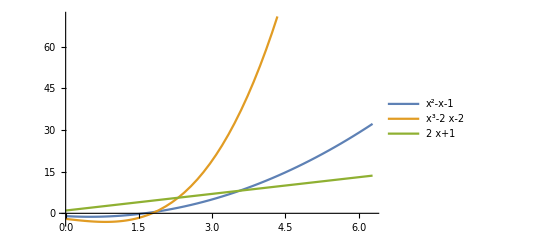

```mathematica
Plot[{x^2-x-1, x^3-2x-2,2x+1},{x,0,2Pi},PlotLegends->"Expressions"]
```

Reproduce the plot from the previous question, but make it so that the background is black, there is a Frame which is styled white, there are no Axes, it has a PlotLabel of “Some interesting functions” and the curves are Orange, LightBlue and Yellow, respectively.

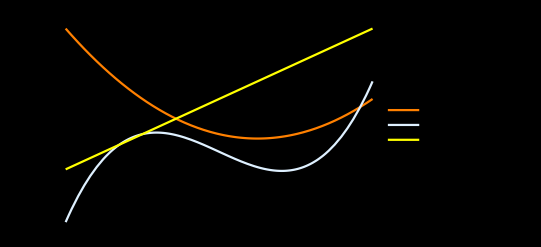

```mathematica
Plot[{x^2-x-1, x^3-2x-2,2x+1}, {x, -2,2}, Background->Black, Frame->True,FrameStyle->White,Axes->False, PlotLabel->x^2-x-1, PlotStyle->{Orange, LightBlue, Yellow}, PlotLegends-> "Expressions"]
```

Reproduce the previous plot, but make it so the first curve is solid, the second is Dashed, and the third is Dotted. Hint: Use Directive to set multiply styles for a curve.

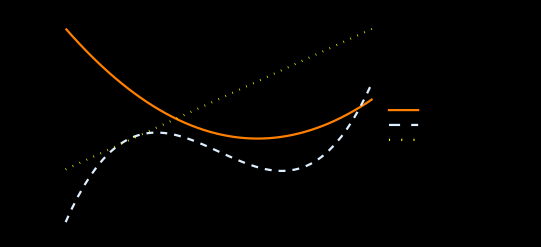

```mathematica
Plot[{x^2-x-1, x^3-2x-2,2x+1}, {x, -2,2}, Background->Black, Frame->True,FrameStyle->White,Axes->False, PlotLabel->x^2-x-1, PlotStyle->{Directive[Orange,Thick], Directive[LightBlue,Dashed], Directive[Yellow,Dotted]},PlotLegends-> "Expressions"]
```

Use Disk and Circle to show display a circle (filled or not filled) centered on x=3, y=2 with radius 4. (Use Show[..., PlotRange→{{-8,8},{-8,8}}] to fix the plot range independently of the parameters of the circle.)

```mathematica
?Circle
```

Circle[{x,y},r] represents a circle of radius r centered at {x,y}.
Circle[{x,y}] gives a circle of radius 1. 
Circle[{x,y},{r_x,r_y}] gives an axis-aligned ellipse with semiaxes lengths r_x and r_y.
Circle[{x,y},…,{θ_1,θ_2}] gives a circular or ellipse arc from angle θ_1 to θ_2.

```mathematica
Manipulate[Show[Graphics[Circle[{x,y},r], Axes->True],PlotRange->{{-8,8},{-8,8}}], {{x,3}}, {{y,2}}, {{r,4}}]
```

```mathematica
?Disk
```

Disk[{x,y},r] represents a disk of radius r centered at {x,y}.
Disk[{x,y}] gives a disk of radius 1. 
Disk[{x,y},{r_x,r_y}] gives an axis-aligned elliptical disk with semiaxes lengths r_x and r_y.
Disk[{x,y},…,{θ_1,θ_2}] gives a sector of a disk from angle θ_1 to θ_2.

```mathematica
Manipulate[Show[Graphics[Disk[{x,y},r], Axes->True], PlotRange->{{-8,8},{-8,8}}], {{x,3}}, {{y,2}}, {{r,4}}]
```

### Manipulate

Create a Manipulate to plot the function a x^3+b x^2+c x+d, where the parameters a, b, c and d are controlled by the Manipulate.

```mathematica
{{Manipulate[Plot[a  x^3+b  x^2+c  x +d,{x,-10,10},PlotRange->20{-1,1}],{{a,1},-10,10},{{b,0},-1,1},{{c,3},0,2π}, {{d,4},0, 5}]}, {□}}
```

{{},{□}}

Create a Manipulate that shows a circle with a control to select whether it is filled (Circle or Disk) and sliders to set the {x,y} coordinates, radius and colour (Hue). (Use Show[..., PlotRange→{{-5,5},{-5,5}}] to keep the plot range while the controls are changed.)

If True, Circle, else Disk

Slider to x,y, radius, color.

Plot Range

```mathematica
Manipulate[Show[Graphics[If[control, {Hue[color],Circle[{x,y},r]}, {Hue[color],Disk[{x,y},r]}], Axes->True],PlotRange->{{-5,5},{-5,5}}], {{x,0}, -10,10}, {{y,0}, 0,5}, {{r,1}, 0,10}, {color, 0,1}, {control,{True, False}}]
```

A simple harmonic oscillator in one dimension has position x(t)=A_x sin(2 π f_x t+ϕ_x), where t is time, A_x is the amplitude, f_x is the frequency and ϕ_x is an arbitrary phase (the last 3 are constants).  A two dimensional simple harmonic oscillator has position (x(t),y(t)) where y(t)=A_y sin(2 π f_y t+ϕ_y) for other constants A_y,f_y and ϕ_y. Write a manipulate that controls the 6 constants and initial and final times and returns a parametric plot of the position of the two dimensional simple harmonic oscillator.

```mathematica
Manipulate[ParametricPlot[{A Sin[2 π fx t+∅x], B Sin[2 π fy -t + ∅y]}, {t,t1,t2}], {t1, 0}, {t2,6}, {A, 1,5}, {fx, 0,5}, {∅x, 0,5},{B, 1,5}, {fy, 0,5}, {∅y, 0,5}]
```

### 2D plots

Display a surface plot of the following function: the magnitude (absolute value) of the sin of z where z is a complex number; the two axes of the surface plot are x and y and z = x + ⅈ y.

```mathematica
z= x+ⅈ y;
```

```mathematica
func[z_] := Abs[Sin[z]];
```

```mathematica
Plot3D[func[z], {x,-5,5}, {y,-5,5}]
```

-Graphics3D-

Recreate the previous plot four times but with a different camera ViewPoint each time (choose Top, Left, Front and {1,3,2}).

```mathematica
Table[Plot3D[func[z], {x, 0,3}, {y,0,3}, ViewPoint->a], {a, {Front, Right, Left, {1,3,2}}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

Create a contour plot of the real part of the ArcSin function as a function of the complex number z. (Hint: use z=x+ⅈ y and plot as a function of x and y).

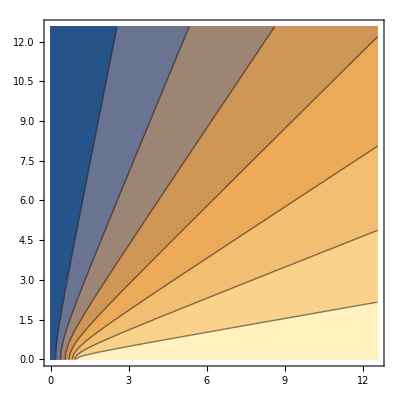

```mathematica
Clear[x,y,z];
z= x+ⅈ y;
new[z_]:= Re[ArcSin[z]];
ContourPlot[new[z], {x,0,4 Pi}, {y,0,4 Pi}]
```